```mathematica
(*Tripple Dot*)
```

```mathematica
(*Spin Matrices*)
σ0=({{1, 0}, {0, 1}});
σx=({{0, 1}, {1, 0}});
σy=({{0, ⅈ}, {-ⅈ, 0}});
σz=({{1, 0}, {0, -1}});
```

```mathematica
(*Majorana operators*)
γx1d=KroneckerProduct[σx,σ0,σ0,σ0,σ0,σ0];
γx1u=KroneckerProduct[σz,σx,σ0,σ0,σ0,σ0];
γx2d=KroneckerProduct[σz,σz,σx,σ0,σ0,σ0];
γx2u=KroneckerProduct[σz,σz,σz,σx,σ0,σ0];
γx3d=KroneckerProduct[σz,σz,σz,σz,σx,σ0];
γx3u=KroneckerProduct[σz,σz,σz,σz,σz,σx];

γy1d=KroneckerProduct[σy,σ0,σ0,σ0,σ0,σ0];
γy1u=KroneckerProduct[σz,σy,σ0,σ0,σ0,σ0];
γy2d=KroneckerProduct[σz,σz,σy,σ0,σ0,σ0];
γy2u=KroneckerProduct[σz,σz,σz,σy,σ0,σ0];
γy3d=KroneckerProduct[σz,σz,σz,σz,σy,σ0];
γy3u=KroneckerProduct[σz,σz,σz,σz,σz,σy];

γx={γx1u,γx1d,γx2u,γx2d,γx3u,γx3d};
γy={γy1u,γy1d,γy2u,γy2d,γy3u,γy3d};

(*Dirac operators*)
dd=Table[1/2(γx[[i]]+ⅈ γy[[i]]),{i,1,6}];
d=Table[1/2(γx[[i]]-ⅈ γy[[i]]),{i,1,6}];
```

```mathematica
(*Parameters*)
α=0.05;  (*Spin Orbit Coupling*)
Δ1=0.2;  (*Induced Superconducing Gap on Dot 1*)
Δ2=0.2;  (*Induced Superconducing Gap on Dot 2*)
Δ3=0.2;  (*Induced Superconducing Gap on Dot 3*)
B=0.0;  (*Magnetic Field*)
t12=-0.1;  (*Hopping* between dots one and two*)
t23=-0.1;  (*Hopping* between dots two and three*)
U=0.01;  (*Electron-Electron interaction*)
ev=0.05;  (*Voltage*)
ϵ1=0.2;  (*Potential for Dot One*)
ϵ2=0.2;  (*Potential for Dot Two*)
ϵ3=0.2;  (*Potential for Dot Three*)
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
t={t12,t12,t23,t23};
Δ={Δ1,Δ1,Δ2,Δ2,Δ3,Δ3};
Eϵ=Table[{},{n,1,2^6}];
```

```mathematica
Eϵ=Table[{},{n,1,2^6}];
nϵ=Table[{},{n,1,2^6}];
Ψl=Table[{},{n,1,2^6}];
gxl={};
gyl={};
For[ϵt=-0.2,ϵt≤0.2,ϵt+=0.01,
ϵ1=ϵt;
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+ Sum[t[[i]](dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]]),{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+ Sum[Δ[[i]](dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]]),{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];
n0=Table[Table[{i,Abs[Conjugate[Ψ[[n]]].dd[[i]].d[[i]].Ψ[[n]]]^2},{i,1,6}],{n,1,Length[Ψ]}];
gx=Table[{i,Abs[Conjugate[Ψ[[2]]].γx[[i]].Ψ[[1]]]^2},{i,1,6}];
gy=Table[{i,Abs[Conjugate[Ψ[[2]]].γy[[i]].Ψ[[1]]]^2},{i,1,6}];

gxl=Join[gxl,{gx}];
gyl=Join[gyl,{gy}];
For[n=1,n≤2^6,n++,
Eϵ[[n]]=Join[Eϵ[[n]],{{ϵt,e[[n]]-e[[1]]}}];
nϵ[[n]]=Join[nϵ[[n]],{n0[[n]]}];
Ψl[[n]]=Join[Ψl[[n]],{Ψ[[n]]}];
];
];
```

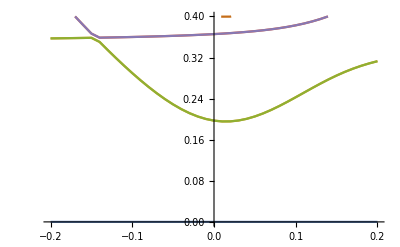

```mathematica
ListPlot[Eϵ,PlotRange->{0.0,2Δ1},Joined->True]
```

```mathematica
Iϵ={};
didv={};
dv=0.01;

For[ϵt=-0.2,ϵt≤0.2,ϵt+=0.02,
ϵ1=ϵt;
ϵ={ϵ1,ϵ1,ϵ2,ϵ2,ϵ3,ϵ3};
(*Hamiltonian*)
Hd3=Sum[ϵ[[i]](dd[[i]].d[[i]]-d[[i]].dd[[i]]),{i,1,6}]+ Sum[t[[i]](dd[[i+2]].d[[i]]+dd[[i]].d[[i+2]]),{i,1,4}]+B Sum[dd[[i+1]].d[[i]]+dd[[i]].d[[i+1]],{i,1,5,2}]+α Sum[dd[[i]].d[[i+3]]+dd[[i+3]].d[[i]]-dd[[i+1]].d[[i+2]]-dd[[i+2]].d[[i+1]],{i,1,4,2}]+ Sum[Δ[[i]](dd[[i+1]].dd[[i]]+d[[i]].d[[i+1]]),{i,1,5,2}]+U Sum[dd[[i]].d[[i]].dd[[i+1]].d[[i+1]],{i,1,5,2}];{e,Ψ}=Transpose[Sort[Transpose[Eigensystem[Hd3]]]];





For[ev=-0.02,ev≤0.4,ev+=0.01,

(*Tempeture and the fermi distribution*)
kb=8.6 10^-5; (*ev/K*)(*need to translate into eigenvalue units*)
T=kb*100;
f[ϵ_]:=1/(ⅇ^(ϵ/T)+1);
(*Hopping to right and left leads*)
tL={-0.1,-0.1,0.0,0.0,0.0,0.0};
tR={0.0,0.0,0.0,0.0,-0.1,-0.1};
bkt[n_,M_,m_]:=Conjugate[Ψ[[n]]].M.Ψ[[m]];
P[ev_]:=Block[{ptp,M,V,PuN,P1,P,Γ,ΓgainL,ΓlossL,ΓgainR,ΓlossR},
ΓgainL=Table[f[e[[n]]-e[[m]]-ev]Sum[tL[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];
ΓlossL=Table[(1-f[e[[m]]-e[[n]]-ev])Sum[tL[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];

ΓgainR=Table[f[e[[n]]-e[[m]]+ev]Sum[tR[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
ΓlossR=Table[(1-f[e[[m]]-e[[n]]+ev])Sum[tR[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
Γ=ΓgainL+ΓlossL+ΓgainR+ΓlossR;
M=Table[Γ[[n,m]]-Sum[KroneckerDelta[n,m]Γ[[l,n]],{l,1,2^6}],{n,2,2^6},{m,2,2^6}];
V=Table[-Γ[[n,1]],{n,2,2^6}];
PuN=Inverse[M].V;
P1=1/(1+Sum[PuN[[n]],{n,1,2^6-1}]);
ptp=Join[{P1},PuN*P1];

ptp
];
Ii[ev_]:=Block[{itp,M,V,PuN,P1,P,Γ,ΓgainL,ΓlossL,ΓgainR,ΓlossR},
ΓgainL=Table[f[e[[n]]-e[[m]]-ev]Sum[tL[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];
ΓlossL=Table[(1-f[e[[m]]-e[[n]]-ev])Sum[tL[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,1,2}],{n,1,2^6},{m,1,2^6}];

ΓgainR=Table[f[e[[n]]-e[[m]]+ev]Sum[tR[[i]]^2 Abs[bkt[n,dd[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
ΓlossR=Table[(1-f[e[[m]]-e[[n]]+ev])Sum[tR[[i]]^2 Abs[bkt[n,d[[i]],m]]^2,{i,5,6}],{n,1,2^6},{m,1,2^6}];
Γ=ΓgainL+ΓlossL+ΓgainR+ΓlossR;
M=Table[Γ[[n,m]]-Sum[KroneckerDelta[n,m]Γ[[l,n]],{l,1,2^6}],{n,2,2^6},{m,2,2^6}];
V=Table[-Γ[[n,1]],{n,2,2^6}];
PuN=Inverse[M].V;
P1=1/(1+Sum[PuN[[n]],{n,1,2^6-1}]);
P=Join[{P1},PuN*P1];
itp=Sum[P[[n]]*Sum[ΓgainL[[m,n]]+ΓlossR[[m,n]]-ΓlossL[[m,n]]-ΓgainR[[m,n]],{m,1,2^6}],{n,1,2^6}];

itp
];
Itp=Ii[ev];
Idv=Ii[ev+dv];
didv0=(Idv-Itp)/dv;
Iϵ=Join[Iϵ,{{ϵt,ev,Itp}}];
didv=Join[didv,{{ϵt,ev,didv0}}];
Print[{ϵt,ev,Itp,didv0}];
];
];
```

{-0.2,-0.02,-1.84797×10^-20,1.28036×10^-18}

{-0.2,-0.01,-5.67609×10^-21,4.22438×10^-19}

{-0.2,0.,-1.45171×10^-21,2.03019×10^-19}

{-0.2,0.01,5.78479×10^-22,2.90454×10^-19}

{-0.2,0.02,3.48301×10^-21,8.16897×10^-19}

{-0.2,0.03,1.1652×10^-20,2.57805×10^-18}

{-0.2,0.04,3.74325×10^-20,4.38463×10^-17}

{-0.2,0.05,4.75895×10^-19,1.33173×10^-16}

{-0.2,0.06,1.80763×10^-18,4.40367×10^-16}

{-0.2,0.07,6.21129×10^-18,1.37347×10^-15}

{-0.2,0.08,1.99459×10^-17,4.35205×10^-15}

{-0.2,0.09,6.34664×10^-17,1.4011×10^-14}

{-0.2,0.1,2.03577×10^-16,4.47181×10^-14}

{-0.2,0.11,6.50758×10^-16,1.43066×10^-13}

{-0.2,0.12,2.08142×10^-15,4.57638×10^-13}

{-0.2,0.13,6.6578×10^-15,1.46397×10^-12}

{-0.2,0.14,2.12975×10^-14,4.68299×10^-12}

{-0.2,0.15,6.81274×10^-14,1.49802×10^-11}

$Aborted

```mathematica
ListPlot[Eϵ,PlotRange->{0.0,2Δ1},Joined->True]
```

-Graphics-

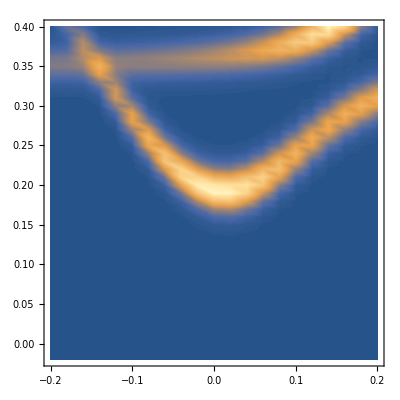

```mathematica
ListContourPlot[didv,PlotRange->All,Contours->100,ContourStyle->None]
```

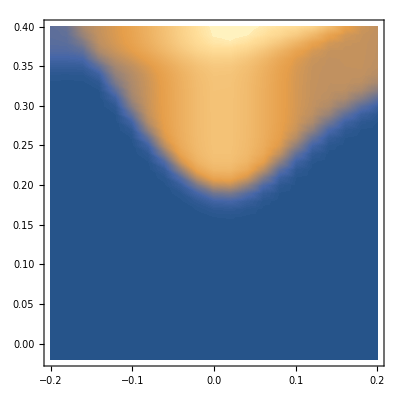

```mathematica
ListContourPlot[Iϵ,PlotRange->All,Contours->100,ContourStyle->None]
```